# Domača naloga – Mathematica

## 1. naloga

1. Izračunajte vsoto ∑_(k=1)^30 k^2/(k+5).
2. Rešite neenačbo:|x-1|≤ 2x+3 
3. Izračunajte drugi odvod funkcije  3tg (2cos(x)+1)  sin (x) in ga poenostavite.
4. S funkcijo FindRoot numerično izračunajte ničlo funkcije  (cos(x))/(e^(x^3-1)) z začetnim približkom x = 1 .

```mathematica
∑_(k=1)^30 k^2/(k+5)
```

189870299151349/525103828704

```mathematica
Abs[x-1]<= 2x+3
Reduce[%,x]
```

Abs[-1+x]≤3+2 x

x≥-2/3

```mathematica
f[x_]:=3Tan[2 Cos[x]+1] Sin[x]
f''[x]
Simplify[f''[x]]
```

-18 Cos[x] Sec[1+2 Cos[x]]^2 Sin[x]-3 Sin[x] Tan[1+2 Cos[x]]+24 Sec[1+2 Cos[x]]^2 Sin[x]^3 Tan[1+2 Cos[x]]

-3 Sin[x] (6 Cos[x] Sec[1+2 Cos[x]]^2+(1-8 Sec[1+2 Cos[x]]^2 Sin[x]^2) Tan[1+2 Cos[x]])

```mathematica
FindRoot[Cos[x]/(E^(x^3-1)),{x,1}]
```

{x→1.5708}

## 2. naloga

1. Definirajte funkciji x(t)=cos(5t) in y(t)=0.5 sin(t).
2. Poiščite take vrednosti t ∈ [0, π], da velja x(t)=0
3. Narišite parametrično podano krivuljo na območju t ∈[0,2π].

Cos[5 t]

0.5 Sin[t]

{{t→π/10},{t→(3 π)/10},{t→π/2},{t→(7 π)/10},{t→(9 π)/10}}

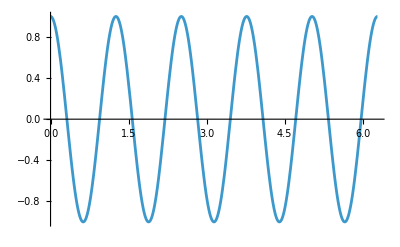

```mathematica
Clear[x]
x[t_]=Cos[5t]
y[t_]=0.5 Sin[t]
Solve[x[t]==0 && 0<=t<=Pi,t]
Plot[
x[t],
{t,0,2Pi}]
```